```mathematica
data=NBodySimulation["InverseSquare",{<|"Mass"->1,"Position"->{0,0},"Velocity"->{0,.5}|>,<|"Mass"->1,"Position"->{1,1},"Velocity"->{0,-.5}|>,<|"Mass"->1,"Position"->{0,1},"Velocity"->{0,0}|>},4]
```

NBodySimulationData[3, <4.>]

```mathematica
ParametricPlot3D[Evaluate[data[All,"Position",t]],{t,0,1}]
```

-Graphics3D-

```mathematica
FacialFeatures[CurrentImage[]]
```

```mathematica
{<|"Image"->,"Age"->32,"Gender"->"Male","Emotion"->Indeterminate|>}
```

```mathematica
ResourceFunction["StopCamera"][]
```

[]

```mathematica
WeatherData["Aberdeen", "WindSpeed"]
```

11.16 km/h

```mathematica
Table[n, {n, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Select[ Table[n, {n, 100}],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Select[ Range[100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Prime[Range[PrimePi[100]]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Range[PrimePi[100]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
Select[ Range[100],Length[Divisors[#]]==2&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

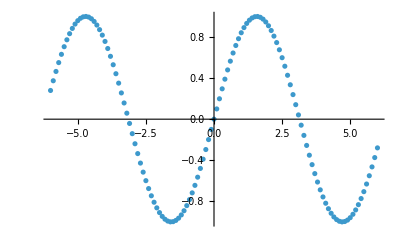

```mathematica
ListPlot[Table[{n, Sin[n]}, {n, -6, 6, 0.1}]]
```

```mathematica
ExampleData[{"TestImage","Couple2"}]
```

-Graphics-

```mathematica
FindTextualAnswer[WikipediaData["Rhinos"], "What the horn of a rhino is made of?"]
```

keratin

```mathematica
Classify["NotablePerson", CurrentImage[]]
```

```mathematica
Entity["Person","FloRida::cyb65"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","FrankOcean::y37b7"]["Image"]
```

-Graphics-

```mathematica
Dataset[EntityValue[Entity["Person","DonaldTrump::6vv3q"],{EntityProperty["Person","FullName"],EntityProperty["Person","BirthDate"],EntityProperty["Person","BirthPlace"]},"PropertyAssociation"]]
```

```mathematica
(#+1)&[9]
```

10

```mathematica
nrst=.
```

```mathematica
nrst:= Nearest[{1,4,6,8,10,15}];
```

```mathematica
nrst[2][[1]]
```

1

```mathematica
nrst[3][[1]]
```

4

```mathematica
Im[3I]
```

3

```mathematica
R[10.2]
```

```mathematica
R[10.2]
```

R[10.2]

```mathematica
√9
```

3

```mathematica
Trace[Plus@@{1,2,3}]
```

{Plus@@{1,2,3},1+2+3,6}

```mathematica
Count[{1,3,5,4, 6.2}, _Integer]
```

4

```mathematica
Take[{1,2,3,4},1]
```

{1}

```mathematica
1//Prime
```

2

```mathematica
Join[{1},{3,4}]
```

{1,3,4}

```mathematica
DeleteDuplicates[{1,3,5,5,4,4, 6.2}]
```

{1,3,5,4,6.2}

```mathematica
PadRight[{1,1,1}, 5, x]
```

{1,1,1,x,x}

```mathematica
Split[{2,2,1,1}]
```

{{2,2},{1,1}}

```mathematica
Outer[f,{1,2},{3,4}]
```

{{f[1,3],f[1,4]},{f[2,3],f[2,4]}}

```mathematica
Partition[{2,2,3,4,5}, 3]
```

{{2,2,3}}

```mathematica
Take[{2,2,3,4,5}, 3]
```

{2,2,3}

```mathematica
Subsets[{2,3,4}]
```

{{},{2},{3},{4},{2,3},{2,4},{3,4},{2,3,4}}

```mathematica
StringPosition["String","Str"][[1]]
```

{1,3}

```mathematica
StringCount["String St r Str2","Str"]
```

2

```mathematica
StringReplace["String", "Str"->"X"]
```

Xing

```mathematica
FreeQ["Str", "Str"]
```

False

```mathematica
Sort[Characters["dcba"]]
```

{a,b,c,d}

```mathematica
DateString[Today]
```

Wed 4 Feb 2026

```mathematica
ToUpperCase["StrinG"]
```

STRING

```mathematica
ToLowerCase["StrinG"]
```

string

```mathematica
CharacterRange["A","Z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
StringMatchQ[" ", WhitespaceCharacter]
```

True

```mathematica
StringSplit["st,rin",","]
```

{st,rin}

```mathematica
StringMatchQ[ToString[x], "x"]
```

True

```mathematica
2^□
```

2^□

```mathematica
2^(2□)
```

```mathematica
2^(2 □2)
```

2^(4 □)

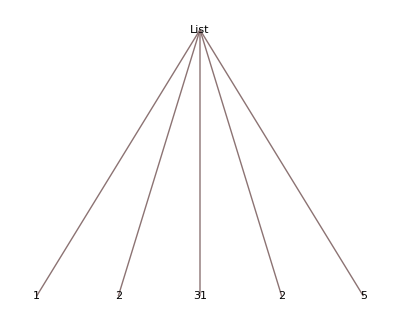

```mathematica
TreeForm[{1,2,31,2,5}]
```

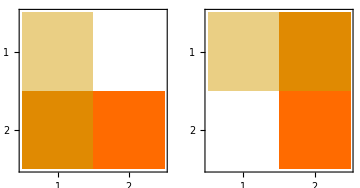

```mathematica
GraphicsRow[{MatrixPlot[{{1,0},{3,4}}],MatrixPlot[Transpose[{{1,0},{3,4}}]]}, ImageSize->Medium]
```

```mathematica
Outer[f,{1,2},{3,4}]
```

{{f[1,3],f[1,4]},{f[2,3],f[2,4]}}

```mathematica
Transpose[{{1,0},{3,4}}][[2]]
```

{0,4}

```mathematica
Transpose[{{1,0},{3,4}}]
```

{{1,3},{0,4}}

```mathematica
TextRecognize[CurrentImage[]]
```

```mathematica
ResourceFunction["StopCamera"]
```

```mathematica
ResourceFunction["StopCamera"][]
```

[]

```mathematica
Transpose[{{1,2,3},{a,b,c}}]
```

{{1,a},{2,b},{3,c}}

```mathematica
(3+#)&[1]
```

4

```mathematica
$LicenseID
```

L4823-8045

```mathematica
$ActivationKey
```

4823-8045-HGYJ6E

```mathematica
TemplateApply["first `a`; second `b`; first `a`",<|"a"->x,"b"->y|>]
```

first x; second y; first x

```mathematica
Interpreter["Chemical"]["Caffeiene"]
```

caffeine

```mathematica
Now
```

Thu 5 Feb 2026 20:00:37GMT

```mathematica
DateString[Now]
```

Thu 5 Feb 2026 20:00:50

```mathematica
DayName[Today]
```

Thursday

```mathematica
MoonPhase[Today, "Icon"]
```

-Graphics-

```mathematica
LocalTime[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
```

Thu 5 Feb 2026 15:05:28GMT-5

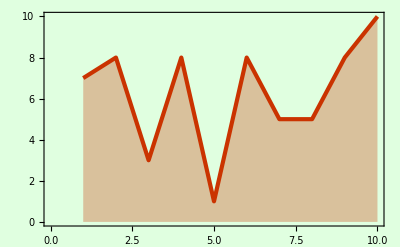

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis,Background->LightGreen]
```

```mathematica
RandomInteger[12,10]
```

{7,0,4,12,9,4,11,2,5,7}

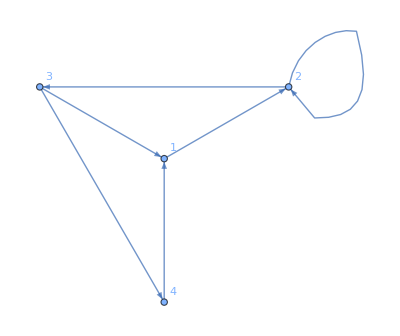
{{{1→2,1→2},{2→3,2→3},{3→4,3→4},{4→1,4→1},{3→1,3→1},{2→2,2→2},{1→2,2→3,3→4,4→1,3→1,2→2}},{VertexLabels→All,VertexLabels→All},{GraphLayout→RadialDrawing,GraphLayout→RadialDrawing},-Graphics-,-Graphics-}

```mathematica
Trace[Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All,GraphLayout->"RadialDrawing"]]
```

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],4,2]
```

{4,1,2}

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

```mathematica
Classify["Sentiment","math can be really easy?" ]
```

Neutral

```mathematica
Options[Classify ]
```

{AcceptanceThreshold→Automatic,AnomalyDetector→None,BatchProcessing→Automatic,ClassPriors→Automatic,ComputedPropertiesMinSampleNumber→1000,DistributionPostProcessing→Automatic,FeatureExtractor→Identity,FeatureNames→Automatic,FeatureTypes→Automatic,FeatureWeights→Automatic,IndeterminateThreshold→Automatic,Method→Automatic,MissingValueSynthesis→Automatic,NominalVariables→Automatic,PerformanceGoal→Automatic,PredictionName→Automatic,ProcessorCaching→True,RandomSeeding→1234,RecalibrationFunction→Automatic,RecordLog→True,TargetDevice→CPU,TieBreakerFunction→RandomChoice,TimeGoal→Automatic,TrainingProgressCheckpointing→None,TrainingProgressReporting→Automatic,TrainingSizeRatio→Automatic,UtilityFunction→Automatic,ValidationSet→Automatic,Weights→Automatic}

```mathematica
Classify[{-Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 0, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 1},
 -Graphics-]
```

1